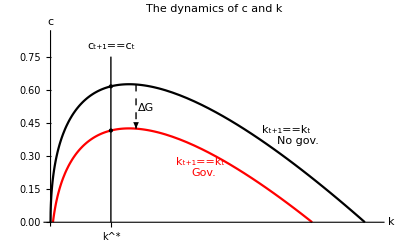

```mathematica
plt4=Plot[{x^0.5-0.4*x,x^0.5-0.4*x-0.2},{x,0,7},PlotRange->{{0,6.5},{0,0.85}},AxesLabel->{"k","c"},Epilog->{Line[{{1.2,0},{1.2,0.75}}],{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},{PointSize[Large],Point[{1.2,#^0.5-0.4*#-0.2&@1.2}]},Text[Subscript["c","t+1"]==Subscript["c","t"],{1.2,0.8}],Text[Subscript["k","t+1"]==Subscript["k","t"],{4.2,(#^0.5-0.4#&@4.2)+0.05},Left],Text["No gov.",{4.2+0.3,(#^0.5-0.4#&@4.2)},Left],{Red,Text[Subscript["k","t+1"]==Subscript["k","t"],{2.5,(#^0.5-0.4#-0.2&@3.5)},Left]},{Red,Text["Gov.",{2.5+0.3,(#^0.5-0.4#-0.2&@3.5)-0.05},Left]},{Arrowheads[Small],Dashed,Arrow[{{1.7,#^0.5-0.4#&@1.7},{1.7,#^0.5-0.4#-0.2&@1.7}}]},Text["ΔG",{1.9,(#^0.5-0.4#&@1.9+#^0.5-0.4#-0.2&@1.9)/2}]},PlotStyle->{Directive[Black],Directive[Red]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["The dynamics of c and k",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/phase_diagram.png",plt4]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/phase_diagram.png

```mathematica
plt5=Plot[{x^0.5-0.4*x,x^0.5-0.4*x-0.2,Piecewise[{{g1[x],0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}],Piecewise[{{g1[x]-0.2,0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}]},{x,0,4},PlotRange->{{0,4},{0,0.85}},AxesLabel->{"k","c"},Epilog->{Line[{{1.2,0},{1.2,0.75}}],{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},{PointSize[Large],Point[{1.2,#^0.5-0.4*#-0.2&@1.2}]},Text[Subscript["c","t+1"]==Subscript["c","t"],{1.2,0.8}],Text[Subscript["k","t+1"]==Subscript["k","t"],{3.2,(#^0.5-0.4#&@3.2)+0.05},Left],{Red,Text[Subscript["k","t+1"]==Subscript["k","t"],{2.5,(#^0.5-0.4#-0.2&@3.5)},Left]},{Arrowheads[Small],Dashed,Arrow[{{1.7,#^0.5-0.4#&@1.7},{1.7,#^0.5-0.4#-0.2&@1.7}}]},Text["ΔG",{1.9,(#^0.5-0.4#&@1.9+#^0.5-0.4#-0.2&@1.9)/2}],{Arrowheads[Small],Dashed,Arrow[BezierCurve[{{1.2,cur1[1.2]},{1,(2*cur1[1]-0.2)/2},{1.2,cur1[1.2]-0.2}}]]}


},PlotStyle->{Directive[Black],Directive[Red]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold]]
```

-Graphics-

```mathematica
cur1[x_]:=x^0.5-0.4*x
```

```mathematica
cur2[x_]:=x^0.5-0.4*x-0.2
```

```mathematica
g[x_]:=a*x^2+b*x+c
```

```mathematica
{a1,b1,c1}={a,b,c}/.FindInstance[{g[1.2]==0.6154,g[1.4]>cur1[1.4],g[1.15]<cur1[1.15],g[0]==0.8*0.6154},{a,b,c,d},Reals][[1]]
```

{0.0854722,0.,0.49232}

```mathematica
g1[x_]:=a1*x^2+b1*x+c1
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/permanent_increase.png",plt5]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/permanent_increase.png

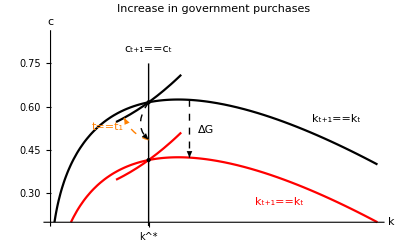

```mathematica
plt6=Plot[{x^0.5-0.4*x,
x^0.5-0.4*x-0.2,
Piecewise[{{g1[x],0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}],
Piecewise[{{g1[x]-0.2,0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}]},{x,0,4},PlotRange->{{0,4},{0.2,0.85}},AxesLabel->{"k","c"},Epilog->
{
Line[{{1.2,0},{1.2,0.75}}],
{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},
{PointSize[Large],Point[{1.2,#^0.5-0.4*#-0.2&@1.2}]},
Text[Subscript["c","t+1"]==Subscript["c","t"],{1.2,0.8}],
Text[Subscript["k","t+1"]==Subscript["k","t"],{3.2,(#^0.5-0.4#&@3.2)+0.05},Left],
{Red,Text[Subscript["k","t+1"]==Subscript["k","t"],{2.5,(#^0.5-0.4#-0.2&@3.5)},Left]},
{Arrowheads[Small],Dashed,Arrow[{{1.7,#^0.5-0.4#&@1.7},{1.7,#^0.5-0.4#-0.2&@1.7}}]},
Text["ΔG",{1.9,(#^0.5-0.4#&@1.9+#^0.5-0.4#-0.2&@1.9)/2}],
{Arrowheads[Small],Dashed,Arrow[BezierCurve[{{1.2,cur1[1.2]},{1,(2*cur1[1]-0.13)/2},{1.2,cur1[1.2]-0.13}}]]},
{Arrowheads[Small],Dashed,Orange,Arrow[BezierCurve[{{1.2,cur1[1.2]-0.13},{1,cur1[1]-0.1},{0.9,g1[0.9]}}]]},
{Orange,Text["t"==Subscript["t",1],{0.9,g1[0.9]-0.032},Right]}


},PlotStyle->{Directive[Black],Directive[Red]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_increase.png",plt6]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_increase.png

```mathematica
{a2,b2,c2}={a,b,c}/.FindInstance[{g[2]==6,g[5]==4.3,(D[g[x],x]<0)/.x-> 5,(D[g[x],x]<0)/.x-> 2},{a,b,c},Reals][[1]];
```

```mathematica
t1[x_]:=a2*x^2+b2*x+c2
```

```mathematica
{a3,b3,c3}={a,b,c}/.FindInstance[{g[5]==4.3,g[8]==6,(D[g[x],x]==0)/.x-> 8},{a,b,c},Reals][[1]];
```

```mathematica
t2[x_]:=a3*x^2+b3*x+c3
```

```mathematica
{a4,b4,c4}={a,b,c}/.FindInstance[{g[2]==3.5,g[5]==4,(D[g[x],x]>0)/.x-> 2,(D[g[x],x,x]>0)/.x-> 2},{a,b,c},Reals][[1]];
```

```mathematica
t3[x_]:=a4*x^2+b4*x+c4
```

```mathematica
{a5,b5,c5}={a,b,c}/.FindInstance[{g[5]==4,g[8]==4.5,(D[g[x],x]==0)/.x-> 8},{a,b,c},Reals][[1]];
```

```mathematica
t4[x_]:=a5*x^2+b5*x+c5
```

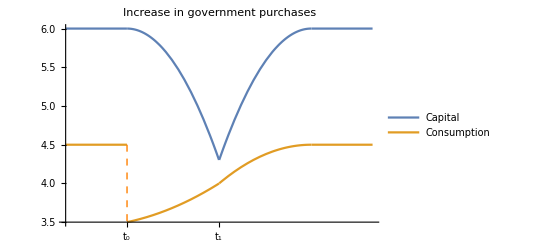

```mathematica
pl7=Plot[{Piecewise[{{6,t<2},{t1[t],2<t<5},{t2[t],5<t<8},{6,t>8}}],
Piecewise[{{4.5,t<2},{t3[t],5>t>2},{t4[t],8>t>5},{4.5,t>8}}]
},{t,0,10},
Epilog-> {
{Dashed,Orange,Line[{{2,4.5},{2,3.5}}]}
},
Ticks->{{{2,Subscript["t","0"]},{5,Subscript["t","1"]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold],
PlotLegends->{"Capital","Consumption"}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_increase_2.png",pl7]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_increase_2.png

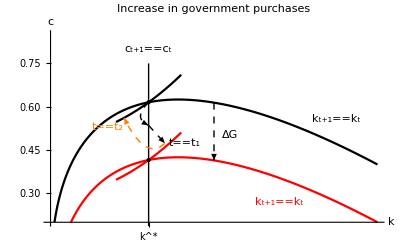

```mathematica
plt8=Plot[{x^0.5-0.4*x,
x^0.5-0.4*x-0.2,
Piecewise[{{g1[x],0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}],
Piecewise[{{g1[x]-0.2,0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}]},{x,0,4},PlotRange->{{0,4},{0.2,0.85}},AxesLabel->{"k","c"},Epilog->
{
Line[{{1.2,0},{1.2,0.75}}],
{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},
{PointSize[Large],Point[{1.2,#^0.5-0.4*#-0.2&@1.2}]},
Text[Subscript["c","t+1"]==Subscript["c","t"],{1.2,0.8}],
Text[Subscript["k","t+1"]==Subscript["k","t"],{3.2,(#^0.5-0.4#&@3.2)+0.05},Left],
{Red,Text[Subscript["k","t+1"]==Subscript["k","t"],{2.5,(#^0.5-0.4#-0.2&@3.5)},Left]},
{Arrowheads[Small],Dashed,Arrow[{{2,#^0.5-0.4#&@2},{2,#^0.5-0.4#-0.2&@2}}]},
Text["ΔG",{2.2,(#^0.5-0.4#&@2.2+#^0.5-0.4#-0.2&@2.2)/2}],
{Arrowheads[Small],Dashed,Arrow[BezierCurve[{{1.2,cur1[1.2]},{1,(2*cur1[1]-0.08)/2},{1.2,cur1[1.2]-0.08}}]]},{Arrowheads[Small],Dashed,Arrow[BezierCurve[{{1.2,cur1[1.2]-0.08},{1.4,cur1[1.4]-0.15}}]]},
{Arrowheads[Small],Dashed,Orange,Arrow[BezierCurve[{{1.4,cur1[1.4]-0.15},{1.2,cur1[1.2]-0.2},{1,cur1[1]-0.1},{0.9,g1[0.9]}}]]},
{Orange,Text["t"==Subscript["t",2],{0.9,g1[0.9]-0.032},Right]},
{Text["t"==Subscript["t",1],{1.45,cur1[1.4]-0.15},Left]}


},PlotStyle->{Directive[Black],Directive[Red]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_an_increase.png",plt8]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_an_increase.png

```mathematica
{a6,b6,c6}={a,b,c}/.FindInstance[{g[0]==6,g[2]==7.3,(D[g[x],x]>0)/.x-> 2,(D[g[x],x]>0)/.x-> 2},{a,b,c},Reals][[1]];
```

```mathematica
t5[x_]:=a6*x^2+b6*x+c6
```

```mathematica
{a7,b7,c7}={a,b,c}/.FindInstance[{g[2]==7.3,g[5]==4.2,(D[g[x],x]<0)/.x-> 2},{a,b,c},Reals][[1]];
```

```mathematica
t6[x_]:=a7*x^2+b7*x+c7
```

```mathematica
{a8,b8,c8}={a,b,c}/.FindInstance[{g[5]==4.2,g[8]==6,(D[g[x],x]>0)/.x-> 5,(D[g[x],x]==0)/.x-> 8},{a,b,c},Reals][[1]];
```

```mathematica
t7[x_]:=a8*x^2+b8*x+c8
```

```mathematica
{a9,b9,c9}={a,b,c}/.FindInstance[{g[0]==3.5,g[4]==2.5,(D[g[x],x]==0)/.x-> 4},{a,b,c},Reals][[1]];
```

```mathematica
t8[x_]:=a9*x^2+b9*x+c9
```

```mathematica
{a10,b10,c10}={a,b,c}/.FindInstance[{g[4]==2.5,g[6]==4.5,(D[g[x],x]==0)/.x-> 6},{a,b,c},Reals][[1]];
```

```mathematica
t9[x_]:=a10*x^2+b10*x+c10
```

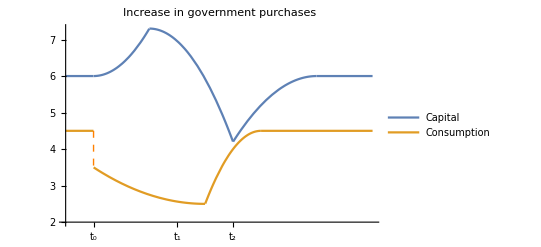

```mathematica
plt9=Plot[{Piecewise[{{6,t<0},{t5[t],t<2},{t6[t],2<t<5},{t7[t],5<t<8},{6,t>8}}],
Piecewise[{{4.5,t<0},{t8[t],0<t<4},{t9[t],4<t<6},{4.5,t>6}}],

},{t,-1,10},AxesOrigin->{-1,2},
Epilog-> {
{Dashed,Orange,Line[{{0,4.5},{0,3.5}}]}
},
Ticks->{{{0,Subscript["t","0"]},{3,Subscript["t","1"]},{5,Subscript["t",2]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold],
PlotLegends->{"Capital","Consumption"}]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_an_increase_2.png",plt9]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/temp_an_increase_2.png

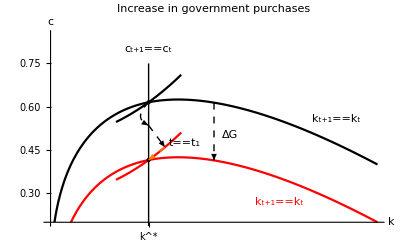

```mathematica
plt10=Plot[{x^0.5-0.4*x,
x^0.5-0.4*x-0.2,
Piecewise[{{g1[x],0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}],
Piecewise[{{g1[x]-0.2,0.8<x<1.6},{-5,x<0.8},{-5,x>1.6}}]},{x,0,4},PlotRange->{{0,4},{0.2,0.85}},AxesLabel->{"k","c"},Epilog->
{
Line[{{1.2,0},{1.2,0.75}}],
{PointSize[Large],Point[{1.2,#^0.5-0.4*#&@1.2}]},
{PointSize[Large],Point[{1.2,#^0.5-0.4*#-0.2&@1.2}]},
Text[Subscript["c","t+1"]==Subscript["c","t"],{1.2,0.8}],
Text[Subscript["k","t+1"]==Subscript["k","t"],{3.2,(#^0.5-0.4#&@3.2)+0.05},Left],
{Red,Text[Subscript["k","t+1"]==Subscript["k","t"],{2.5,(#^0.5-0.4#-0.2&@3.5)},Left]},
{Arrowheads[Small],Dashed,Arrow[{{2,#^0.5-0.4#&@2},{2,#^0.5-0.4#-0.2&@2}}]},
Text["ΔG",{2.2,(#^0.5-0.4#&@2.2+#^0.5-0.4#-0.2&@2.2)/2}],
{Arrowheads[Small],Dashed,Arrow[BezierCurve[{{1.2,cur1[1.2]},{1,(2*cur1[1]-0.08)/2},{1.2,cur1[1.2]-0.08}}]]},{Arrowheads[Small],Dashed,Arrow[BezierCurve[{{1.2,cur1[1.2]-0.08},{1.4,g1[1.4]-0.2
}}]]},
{Arrowheads[Small],Dashed,Orange,Arrow[BezierCurve[{{1.4,g1[1.4]-0.2},{1.2,g1[1.2]-0.2}}]]},

{Text["t"==Subscript["t",1],{1.45,cur1[1.4]-0.15},Left]}


},PlotStyle->{Directive[Black],Directive[Red]},Ticks->{{{1.2,Superscript["k","*"]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold]]
```

```mathematica
Export["/home/eric/eric-roca.github.io/static/img/ramsey_gov/perm_an_increase.png",plt10]
```

/home/eric/eric-roca.github.io/static/img/ramsey_gov/perm_an_increase.png

```mathematica
{a11,b11,c11}={a,b,c}/.FindInstance[{g[0]==6,g[2]==7.3,(D[g[x],x]>0)/.x-> 2,(D[g[x],x]>0)/.x-> 2},{a,b,c},Reals][[1]];
```

```mathematica
t10[x_]:=a11*x^2+b11*x+c11
```

```mathematica
{a12,b12,c12}={a,b,c}/.FindInstance[{g[2]==7.3,g[5]==5.3,(D[g[x],x]<0)/.x-> 2,(D[g[x],x]==0)/.x-> 5},{a,b,c},Reals][[1]];
```

```mathematica
t11[x_]:=a12*x^2+b12*x+c12
```

```mathematica
{a13,b13,c13}={a,b,c}/.FindInstance[{g[0]==3.5,g[2]==3,(D[g[x],x]<0)/.x-> 2},{a,b,c},Reals][[1]];
```

```mathematica
t12[x_]:=a13*x^2+b13*x+c13
```

```mathematica
{a14,b14,c14}={a,b,c}/.FindInstance[{g[2]==3,g[5]==2.5,(D[g[x],x]==0)/.x-> 5},{a,b,c},Reals][[1]];
```

```mathematica
t13[x_]:=a14*x^2+b14*x+c14
```

```mathematica
{a10,b10,c10}={a,b,c}/.FindInstance[{g[4]==2.5,g[6]==4.5,(D[g[x],x]==0)/.x-> 6},{a,b,c},Reals][[1]];
```

```mathematica
t9[x_]:=a10*x^2+b10*x+c10
```

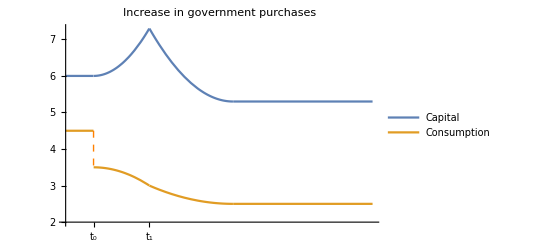

```mathematica
plt9=Plot[{Piecewise[{{6,t<0},{t10[t],t<2},{t11[t],2<t<5},{5.3,t>5}}],
Piecewise[{{4.5,t<0},{t12[t],0<t<2},{t13[t],2<t<5},{2.5,t>5}}]

},{t,-1,10},AxesOrigin->{-1,2},
Epilog-> {
{Dashed,Orange,Line[{{0,4.5},{0,3.5}}]}
},
Ticks->{{{0,Subscript["t","0"]},{2,Subscript["t","1"]}},{None}},PlotLabel->Style["Increase in government purchases",Black,Larger,Bold],
PlotLegends->{"Capital","Consumption"}]
```